# Gerik Zatorski ME 454 Final

```mathematica
Quit[];
```

## Stage 1 - Ball is stuck to hand

ListInterpolation::inhr: Requested order is too high; order has been reduced to {1}.

-π/90

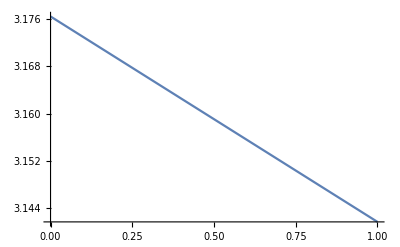

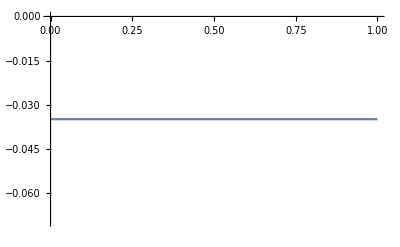

```mathematica
ClearAll["Global`*"]

(***************************************************************************)
(* Helper Functions *)
(***************************************************************************)

(* SE(2) representation of rigid body motion in the plane *)
g[x_,y_,θ_]={{Cos[θ],-Sin[θ],x},{Sin[θ],Cos[θ],y},{0,0,1}};
(* unhat takes a 3x3 matrix that is assumed to be ginv.gdot for SE(2) and returns a 3x1 vector. The first two components are the linear velocities in x and y and the third component is the angular velocity (around the "z" axis that is out of the plane of motion *)
unhat[a_]:={a[[1,3]],a[[2,3]],a[[2,1]]};
(* hat[] takes a 3x1 vector and creates a 3x3 matrix *)
hat[a_]:={{0,-a[[3]],a[[1]]},{a[[3]],0,a[[2]]},{0,0,0}};
(* Hom[] takes a point in the plane and adds a 1 to the end of it to create a homogeneous representation of that point. This is used for animation *)
Hom[pt_]:=Flatten[{pt,1}];
(* UnHom[] takes a homogeneous representation of a point and returns the point in the plane by removing the 1 at the end *)
UnHom[pt_]:={pt[[1]],pt[[2]]};
(* Distance between two points in 2D plane *)
Distance2D[x_,y_]:=Sqrt[(x[[1]]-y[[1]])^2+(x[[2]]-y[[2]])^2];
(* useful for debugging ... *)
headlist={Or,And,Equal,Unequal,Less,LessEqual,Greater,GreaterEqual,Inequality};
getAllVariables[f_?NumericQ]:=Sequence[]
getAllVariables[{}]:=Sequence[]
getAllVariables[t_]/;MemberQ[headlist,t]:=Sequence[]
getAllVariables[ll_List]:=Flatten[Union[Map[getAllVariables[#]&,ll]]]
getAllVariables[Derivative[n_Integer][f_][arg__]]:=getAllVariables[{arg}]
getAllVariables[f_Symbol[arg__]]:=Module[{fvars},If[MemberQ[Attributes[f],NumericFunction]||MemberQ[headlist,f],fvars=getAllVariables[{arg}],(*else*)fvars=f[arg]];
fvars]
getAllVariables[other_]:=other
extractVariables[formula_]:=With[{pat=_Symbol[___][___]|Subscript[_Symbol,__][___]|Subscript[_Symbol,__]|_Symbol},Union@Cases[formula,pat,-1]]

(***************************************************************************)
(* Problem Setup *)
(***************************************************************************)

(* Constants *)
FtToM=0.3048;
m=0.625;
diameterBall=9.55/12*FtToM;
rball=diameterBall/2;
tMax =1;

(* Robot Link Lengths Constants *)
Lhand=0.3048*8.5/12;

(***************************************************************************)
(* Frame Transformations *)
(***************************************************************************)

(* World to Joint Frame Transformations *)
gwrist=g[2,0,0].g[0,0,θwrist[t]];
ghand=gwrist.g[Lhand/2,0,0];
gfingertip=gwrist.g[Lhand,0,0].g[0,0,0];

(* World to Ball Frame Transformations prior to roll*)
gballbefore=gwrist.g[Lhand/2,-rball,0];
gline1before=gballbefore.g[-rball,0,0];
gline2before=gballbefore.g[rball,0,0];

(***************************************************************************)
(* Joint Velocity Trajectories *)
(***************************************************************************)

θwristsol=ListInterpolation[{Pi*182/180,Pi*180/180},{0,tMax}][t];
(*θwristsol=ListInterpolation[{Pi*21/16,Pi*21/16},{0,tMax}][t];*)
(*θwristsol=Interpolation[Table[{{t},-3*Sin[t]+Pi*21/16,-Cos[t]},{t,0,2,0.05}]][t]*)
θwristdotsol=D[θwristsol,t];
θwristdotdotsol=D[θwristdotsol,t];

(* gotta do this *)
θwrist[t]=θwristsol;
θwrist'[t]=θwristdotsol;
θwrist''[t]=θwristdotdotsol;

(***************************************************************************)
(* Plots and Animation *)
(***************************************************************************)

coordwrist[time_]:=({gwrist[[1,3]],gwrist[[2,3]]})/.t->time;
coordfingertip[time_]:=({gfingertip[[1,3]],gfingertip[[2,3]]}/.{θwrist[t]->θwristsol})/.t->time;
coordballbefore[time_]:=({gballbefore[[1,3]],gballbefore[[2,3]]}/.{θwrist[t]->θwristsol})/.t->time;
coordline1before[time_]:=({gline1before[[1,3]],gline1before[[2,3]]}/.{θwrist[t]->θwristsol})/.t->time;
coordline2before[time_]:=({gline2before[[1,3]],gline2before[[2,3]]}/.{θwrist[t]->θwristsol})/.t->time;

(* Link Graphics *)
Graphicshand=Line[{coordwrist[t],coordfingertip[t]}];

(* Ball Graphics *)
Graphicsballbefore = Circle[coordballbefore[t],rball];
Graphicsballlinebefore=Line[{coordline1before[t],coordline2before[t]}];

(* Solving for conditions at beginning of roll *)
troll=0;
tr=gballbefore/.{θwrist[t]->θwristsol};
xr=tr[[1,3]]/.t->troll;
yr=tr[[2,3]]/.t->troll;
θr=θwrist[t]/.{θwrist[t]->θwristsol}/.t->troll;
(*θr=N[ArcCos[tr[[1,1]]]];*)

(* dot sol estimation *)
(*tr1=gballbefore/.{θwrist[t]->θwristsol}/.t->(troll-.01);
tr2=gballbefore/.{θwrist[t]->θwristsol}/.t->(troll+.01);
θrdot=N[(ArcCos[tr2[[1,1]]]-ArcCos[tr1[[1,1]]])/.02]
xrdot=N[(tr2[[1,3]]-tr1[[1,3]])/.02]
yrdot=N[(tr2[[2,3]]-tr1[[2,3]])/.02]*)
(*θrdot=N[(ArcCos[tr2[[1,1]]]-ArcCos[tr[[1,1]]])/.01]
xrdot=N[(tr2[[1,3]]-tr[[1,3]])/.01]
yrdot=N[(tr2[[2,3]]-tr[[2,3]])/.01]*)

(* dot sol exact *)
θrdot=θwristdotsol/.t->troll
trdot=D[gballbefore,t]/.{θwrist[t]->θwristsol,θwrist'[t]->θwristdotsol};
(*trdot=D[gballbefore,t];*)
xrdot=trdot[[1,3]]/.t->troll;
yrdot=trdot[[2,3]]/.t->troll;

(* Plots *)
Plot[θwristsol,{t,0,tMax}]
Plot[θwristdotsol,{t,0,tMax}]

(* Animations *)
Animate[
Show[
Graphics[{
Black,Graphicshand/.t->time,
Black,Graphicsballbefore/.t->time,
Black,Graphicsballlinebefore/.t->time
},Axes->True]
],
{time,0,tMax},
AnimationRunning->False,
AnimationRate->1.0
]
```

## Stage 2 - Ball rolls on hand (constrained to maintain hand contact)

```mathematica
(* New Ball Frame Transforms for time after roll *)
gball=g[x[t],y[t],0].g[0,0,θ[t]];
ghandball=Inverse[ghand].gball; (* ball in hand frame *)
θhandball=θ[t]-θwrist[t];
xhandball=ghandball[[1,3]];
gcontact=gwrist.g[Lhand/2-rball*θhandball,0,0];

(* Point of contact *)
mhand=(gfingertip[[2,3]]-gwrist[[2,3]])/(gfingertip[[1,3]]-gwrist[[1,3]]);
Eqhand=contacty-gfingertip[[2,3]]==mhand*(contactx-gfingertip[[1,3]]);
Eqprojection=contacty-gball[[2,3]]==-1/mhand*(contactx-gball[[1,3]]);
contacttemp=Solve[{Eqhand&&Eqprojection},{contactx,contacty}];
contactx=contacttemp[[1,1,2]];
contacty=contacttemp[[1,2,2]];
 
(* Ball Configuration Variables *)
q={{x[t],y[t],θ[t]}}ᵀ;
dq=D[q,t];
ddq=D[dq,t];

(* Lagrangian using body velocities (see lecture 23) *)
Vball=unhat[Inverse[gball].D[gball,t]];
Iball=DiagonalMatrix[{m,m,m*rball^2}];
(*J=m*rball^2;*)
KE=1/2*(Vball.Iball).{Vball}ᵀ;
PE=m*grav*y[t];
Lag =KE-PE;

(***************************************************************************)
(* Constraints and External forces *)
(***************************************************************************)

(* Constraints *)
(* Ball remains in contact with last link *)
ϕa=ghandball[[2,3]]+rball;

(* Ball rolls without slipping where x=rball*θ *)
ϕb=xhandball-rball*θhandball;

(***************************************************************************)
(* Euler-Lagrange equations VECTORS *)
(***************************************************************************)

(* BOTH constraints *)
Eq1=D[D[Lag,x'[t]],t]-D[Lag,x[t]]==λa*D[ϕa,x[t]]+λb*D[ϕb,x[t]];
Eq2=D[D[Lag,y'[t]],t]-D[Lag,y[t]]==λa*D[ϕa,y[t]]+λb*D[ϕb,y[t]];
Eq3=D[D[Lag,θ'[t]],t]-D[Lag,θ[t]]==λa*D[ϕa,θ[t]]+λb*D[ϕb,θ[t]];
Eq4=D[D[ϕa,t],t]==0;
Eq5=D[D[ϕb,t],t]==0;

(* ODEs *)
ELtemp=Solve[{Eq1&&Eq2&&Eq3&&Eq4&&Eq5},{x''[t],y''[t],θ''[t],λa,λb}];
EL={x''[t]==ELtemp[[1,1,2]],y''[t]==ELtemp[[1,2,2]],θ''[t]==ELtemp[[1,3,2]]};

(* Constants and Initial Condition *)
grav = 9.8;
InitCon={x[troll]==xr,y[troll]==yr,θ[troll]==θr,x'[troll]==xrdot,y'[troll]==yrdot,θ'[troll]==θrdot};

(***************************************************************************)
(* Numerical Solutions for Desired Trajectories *)
(***************************************************************************)

(*sol=NDSolve[Join[EL,InitCon],{x,y,θ},{t,troll,tMax}];*)
(*sol=NDSolve[Join[EL,InitCon],{x,y,θ},{t,troll,tMax},
Method->{"ExplicitRungeKutta","DifferenceOrder"->4}];*)
(*θhandball/.t->0*)

Jwrist=θwristsol/.t->time;
tRelease=tMax; 
sol=NDSolve[Join[EL,InitCon,
(* determine time of release *)
{WhenEvent[rball*(θ[t]-Jwrist/.time->t)>Lhand/2,
{Print["Let it fly!"],tRelease=t,Print[tRelease],"StopIntegration"},
"DetectionMethod"->"Sign"]}
],{x,y,θ},{t,troll,tMax},
Method->{"ExplicitRungeKutta","DifferenceOrder"->3}];

xsol=x[t]/.sol;
ysol=y[t]/.sol;
θsol=θ[t]/.sol;

(***************************************************************************)
(* PLOTS AND ANIMATION *)
(***************************************************************************)

(*Plot[ϕa/.{θwrist[t]->θwristsol,x[t]->xsol,y[t]->ysol,θ[t]->θsol},{t,troll,tRelease},PlotLabel->"ϕa constraint"]
Plot[ϕb/.{θwrist[t]->θwristsol,x[t]->xsol,y[t]->ysol,θ[t]->θsol},{t,troll,tRelease},PlotLabel->"ϕb constraint"]
Plot[(xhandball)/.{θwrist[t]->θwristsol,x[t]->xsol,y[t]->ysol,θ[t]->θsol},{t,troll,tRelease},PlotLabel->"xhandball"]
Plot[θhandball/.{θwrist[t]->θwristsol,x[t]->xsol,y[t]->ysol,θ[t]->θsol},{t,troll,tRelease},PlotLabel->"ball angle relative to hand"]*)
(*Plot[x[t]/.{θwrist[t]->θwristsol,x[t]->xsol,y[t]->ysol,θ[t]->θsol},{t,troll,tRelease},PlotLabel->"x[t]"]
Plot[y[t]/.{θwrist[t]->θwristsol,x[t]->xsol,y[t]->ysol,θ[t]->θsol},{t,troll,tRelease},PlotLabel->"y[t]"]
Plot[θ[t]/.{θwrist[t]->θwristsol,x[t]->xsol,y[t]->ysol,θ[t]->θsol},{t,troll,tRelease},PlotLabel->"θ[t]"]*)

(* Dynamic coords and graphics *)
coordball[time_]:=({gball[[1,3]],gball[[2,3]]}/.{θwrist[t]->θwristsol,x[t]->xsol,y[t]->ysol,θ[t]->θsol})/.t->time;
coordcontact[time_]:=({contactx,contacty}/.{θwrist[t]->θwristsol,x[t]->xsol,y[t]->ysol,θ[t]->θsol})/.t->time;
gmidline1=gball.g[-rball,0,0];
gmidline2=gball.g[rball,0,0];
coordmidline1[time_]:=({gmidline1[[1,3]],gmidline1[[2,3]]}/.{θwrist[t]->θwristsol,x[t]->xsol,y[t]->ysol,θ[t]->θsol})/.t->time;
coordmidline2[time_]:=({gmidline2[[1,3]],gmidline2[[2,3]]}/.{θwrist[t]->θwristsol,x[t]->xsol,y[t]->ysol,θ[t]->θsol})/.t->time;
Graphicsball = Circle[{coordball[t][[1]][[1]],coordball[t][[2]][[1]]},rball];
Graphicscontact=Locator[{coordcontact[t][[1]][[1]],coordcontact[t][[2]][[1]]}];
Graphicsballline=Line[{{coordmidline1[t][[1]][[1]],coordmidline1[t][[2]][[1]]},{coordmidline2[t][[1]][[1]],coordmidline2[t][[2]][[1]]}}];

Animate[
Show[
Graphics[{
Black,Graphicshand/.t->time,
Black,Graphicsball/.t->time,
Black,Graphicsballline/.t->time,
Graphicscontact/.t->time
}],
(*PlotRange->{{-1,8},{-1,8}},*)
Axes->True
],
{time,troll,tRelease},
AnimationRunning->False,
AnimationRate->1.0
]
```

## Optimizing Control (Balancing Ball)

```mathematica
(* Constants *)
g=9.81;
h=1;
T=tMax - 0.1;

(***************************************************************************)
(* Control Dynamics *)
(***************************************************************************)
(* x,y correspond to ball, θ corresponds to bar *)

X={{x[t]},{y[t]},{θ[t]},{x'[t]},{y'[t]},{θ'[t]}};
dX=D[X,{t,1}];
U={{wristAccel[t]}};

xd[t_]:=0//N;
yd[t_]:=0//N;
θd[t_]:=0//N;
dxd[t_]:=D[θd[t],t]//N;
dyd[t_]:=D[θd[t],t]//N;
dθd[t_]:=D[θd[t],t]//N;
Xd[t_]:={{xd[t]},{yd[t]},{θd[t]},{dxd[t]},{dyd[t]},{dθd[t]}};

(* ODE for state evolution *)
f[x_,u_]:={
{x[[4,1]]},
{x[[5,1]]},
{x[[6,1]]},
{ELtemp[[1,1,2]]},
{ELtemp[[1,2,2]]},
{ELtemp[[1,3,2]]}
};

(***************************************************************************)
(* Cost Function Stuff *)
(***************************************************************************)

(*Subscript[Q, r]=Subscript[Q, n]=Q={{100,0},{0,100}};
Subscript[R, r]=Subscript[R, n]=R={{0.001}};
Subscript[P1, r]=Subscript[P1, n]=P1={{0,0},{0,0}};*)
Qval=10^-3;
Rval=10^3;
P1val=10^0;
Subscript[Q, r]=Subscript[Q, n]=Q=DiagonalMatrix[{Qval,Qval,Qval,Qval,Qval,Qval}];
Subscript[R, r]=Subscript[R, n]=R=DiagonalMatrix[{Rval}];
Subscript[P1, r]=Subscript[P1, n]=P1=DiagonalMatrix[{P1val,P1val,P1val,P1val,P1val,P1val}];

L[X_,U_]:=1/2((X-Xd[t])ᵀ.Q.(X-Xd[t]))+1/2Uᵀ.R.U;
J[X_,U_]:=Quiet[NIntegrate[L[X,U],{t,0,T},Method->{Automatic,"SymbolicProcessing"->False}]]+1/2((X-Xd[t])/.t->T)ᵀ.P1.((X-Xd)/.t->T);
DJzeta[xi_,zeta_]:=Module[{X=xi[[1]],U=xi[[2]],z=zeta[[1]],v=zeta[[2]]},Return[Quiet[NIntegrate[(Q.(X-Xd[t]))ᵀ.z+(R.U)ᵀ.v,{t,0,T},Method->{Automatic,"SymbolicProcessing"->False}]]+((P1.(X-Xd[t]))ᵀ.z)/.t->T];
];
Subscript[xibar, 0]={Xd[t],{{0}}};
(*Subscript[xi, 0]={{{0},{0}},{{0}}};*)
Subscript[xi, 0]={{{0},{0},{0},{0},{0},{0}},{{0}}};
Subscript[P1, r]=Subscript[P1, n]=P1=ConstantArray[0,{6,6}];

(***************************************************************************)
(* Symbolic Helpers *)
(***************************************************************************)

Asym=D[(f[X,U]),Xᵀ];
Bsym=D[f[X,U],Uᵀ];
asym=D[L[X,U],{X,1}][[1,1]];
bsym=D[L[X,U],U][[1]];
(* Transform A and B to the proper size *)
Ta[R_]:=Table[R[[i,1]],{i,1,Length@X}];

(***************************************************************************)
(* Control Related Functions *)
(***************************************************************************)

(* Riccati solution for P *)
Psol[A_,B_,Q_,R_,P1_]:=Module[{PEQ1,PEQ2,Ps,i,j},
Ri[t_]:=Table[Subscript[P, i,j][t],{i,1,Length@X},{j,1,Length@X}];
PEQ1=(Ri'[t]+Aᵀ.Ri[t]+Ri[t].A-Ri[t].B.Inverse[R].Bᵀ.Ri[t]+Q)==ConstantArray[0,{Length@X,Length@X}];
PEQ2=Ri[T]==P1;
Ps=(NDSolve[{PEQ1,PEQ2},Flatten[Ri[t]],{t,0,T}])[[1]];
Return[(Ri[t]/.Ps)];
];

(* Riccati solution for r *)
rsol[A_,B_,a_,b_,P_,R_,P1_]:=Module[{rEQ1,rEQ2,rs},
(* todo later: make this robust to different sizes *)
(*Rir[t_]:=Table[{Subscript[r, i][t]},{i,1,Length@X}];*)

Rir[t_]:={{r1[t]},{r2[t]},{r3[t]},{r4[t]},{r5[t]},{r6[t]}};
rEQ1=Rir'[t]+(A-B.Inverse[R].Bᵀ.P)ᵀ.Rir[t]+a-P.B.Inverse[R].b=={{0},{0},{0},{0},{0},{0}};
(*rEQ1=Rir'[t]+(A-B.Inverse[R].Bᵀ.P)ᵀ.Rir[t]+a-P.B.Inverse[R].b==ConstantArray[0,{Length@X,1}];*)
rEQ2=Rir[T]==(P1.(X-Xd[t]))/.t->T;
rs=(NDSolve[{rEQ1,rEQ2},Flatten[Rir[t]],{t,0,T}])[[1]];

(* todo: debug this problem when P1 is given value *)
(*Print["X = ",X];
Print["Xd[t] = ",Xd[t]];
Print["rEQ2 = ",rEQ2];*)

Return[(Rir[t]/.rs)];
];

(* Descent direction solution *)
zsol[A_,B_,b_,P_,r_]:=Module[{v,zEQ1,zEQ2,zs,zMat,dzMat},
(* todo: make this robust to different sizes *)
zMat[t_]:={{z1[t]},{z2[t]},{z3[t]},{z4[t]},{z5[t]},{z6[t]}};
dzMat[t_]:=D[zMat[t],t];
v=-Inverse[Subscript[R, n]].(b+Bᵀ.P.zMat[t]+Bᵀ.r);
zEQ1=dzMat[t]==A.zMat[t]+B.v;
zEQ2=zMat[0]==ConstantArray[0,{Length@X,1}];
zs=(NDSolve[{zEQ1,zEQ2},Flatten[dzMat[t]],{t,0,T}])[[1]];
Return[({{z1[t]},{z2[t]},{z3[t]},{z4[t]},{z5[t]},{z6[t]}}/.zs)];
];

(* Projection of xibar onto feasible space *)
Proj[xibar_,K_]:=Module[{xbar=xibar[[1]],ubar=xibar[[2]],xEQ1,xEQ2,xs},
(* TODO later: update this to accomodate variable state/control spaces *)
(*xEQ1={
dX[[4]]==(f[X,U]/.wristAccel[t]->(ubar+K.(X-xbar))[[1,1]])[[4]];
dX[[5]]==(f[X,U]/.wristAccel[t]->(ubar+K.(X-xbar))[[1,1]])[[5]];
dX[[6]]==(f[X,U]/.wristAccel[t]->(ubar+K.(X-xbar))[[1,1]])[[6]];
};*)

xEQ1={dX[[4]],dX[[5]],dX[[6]]}=={
(f[X,U]/.wristAccel[t]->(ubar+K.(X-xbar))[[1,1]])[[4]],
(f[X,U]/.wristAccel[t]->(ubar+K.(X-xbar))[[1,1]])[[5]],
(f[X,U]/.wristAccel[t]->(ubar+K.(X-xbar))[[1,1]])[[6]]
};

xEQ2={{x[0]},{y[0]},{θ[0]},{x'[0]},{y'[0]},{θ'[0]}}=={{0},{0},{0},{0},{0},{0}};
(*xs=(NDSolve[{xEQ1,xEQ2},{θ[t],θ'[t]},{t,0,T}])[[1]];*)
xs=(NDSolve[{xEQ1,xEQ2},{x[t],y[t],θ[t],x'[t],y'[t],θ'[t]},{t,0,T}])[[1]];

(*Print["xEQ1 = ",xEQ1];
Print["xEQ2 = ",xEQ2];*)

Return[(X/.xs)];
];

(* Armijo line search *)
Armijo[xi_,xibar_,zeta_,K_,maxIters_:100]:=Module[{α=0.0001,β=0.5,n=0,xibarn,γ,X,U,Xn,Un},
X=xi[[1]];
U=xi[[2]];
γ=β^n;
xibarn=xibar+γ*zeta;
Xn=Proj[xibarn,K];
Un=xibarn[[2]]+K.(Xn-xibarn[[1]]);
While[And[(J[Xn,Un])[[1,1]]>(J[X,U]+α*γ*DJzeta[xi,zeta])[[1,1]],n<maxIters],
n=n+1;
γ=β^n;
xibarn=xibar+γ*zeta;
Xn=Proj[xibarn,K];
Un=xibarn[[2]]+K.(Xn-xibar[[1]]);
];
Return[{xibarn,{Xn,Un}}];
];

(***************************************************************************)
(* Alogrithm Loop *)
(***************************************************************************)

ϵ=10^-3;
i=0;
Subscript[norm, 0]=100;

While[And[Abs[Subscript[norm, i]]>ϵ,i<30],
(* TODO: update for balancing problem *)
{Subscript[A, i],Subscript[B, i],Subscript[a, i],Subscript[b, i]}={Ta[Asym],Ta[Bsym],asym,bsym}/.{
x[t]->Subscript[xi, i][[1,1,1]],
y[t]->Subscript[xi, i][[1,2,1]],
θ[t]->Subscript[xi, i][[1,3,1]],
x'[t]->Subscript[xi, i][[1,4,1]],
y'[t]->Subscript[xi, i][[1,5,1]],
θ'[t]->Subscript[xi, i][[1,6,1]],
wristAccel[t]->Subscript[xi, i][[2,1,1]]
};

Subscript[Pn, i]=Psol[Subscript[A, i],Subscript[B, i],Subscript[Q, n],Subscript[R, n],Subscript[P1, n]];
Subscript[r, i]=rsol[Subscript[A, i],Subscript[B, i],Subscript[a, i],Subscript[b, i],Subscript[Pn, i],Subscript[R, n],Subscript[P1, n]];
Subscript[z, i]=zsol[Subscript[A, i],Subscript[B, i],Subscript[b, i],Subscript[Pn, i],Subscript[r, i]];

Subscript[v, i]=-Inverse[Subscript[R, n]].(Subscript[b, i]+Subscript[B, i] ᵀ.Subscript[Pn, i].Subscript[z, i]+Subscript[B, i] ᵀ.Subscript[r, i]);
Subscript[zeta, i]={Subscript[z, i],Subscript[v, i]};
Subscript[Pr, i]=Psol[Subscript[A, i],Subscript[B, i],Subscript[Q, r],Subscript[R, r],Subscript[P1, r]];
Subscript[κ, i]=-Inverse[Subscript[R, r]].Subscript[B, i] ᵀ.Subscript[Pr, i];
{Subscript[xibar, i+1],Subscript[xi, i+1]}=Armijo[Subscript[xi, i],Subscript[xibar, i],Subscript[zeta, i],Subscript[κ, i]];
Subscript[norm, i+1]=(DJzeta[Subscript[xi, i],Subscript[zeta, i]])[[1,1]];
i=i+1;
];
```

## Plots And Animation

```mathematica
xsol=Subscript[xi, i][[1]][[1,1]];
ysol=Subscript[xi, i][[1]][[2,1]];
θwristsol=Subscript[xi, i][[1]][[3,1]];

(* Plot trajectories and control effort *)
(*Plot[Subscript[xi, i],{t,0,T},PlotRange->Full]*)
(*Plot[Subscript[xi, i][[1]][[3,1]],{t,0,T},PlotRange->Full]*)

(* Dynamic coords and graphics *)
coordball[time_]:=({gball[[1,3]],gball[[2,3]]}/.{θwrist[t]->θwristsol,x[t]->xsol,y[t]->ysol,θ[t]->θsol})/.t->time;
Graphicsball = Circle[{coordball[t][[1]][[1]],coordball[t][[2]][[1]]},rball];

Animate[
Show[
Graphics[{
Black,Graphicshand/.t->time,
Black,Graphicsball/.t->time
}],
PlotRange->{{1,2.5},{-0.5,1}},
Axes->True
],
{time,troll,tRelease},
AnimationRunning->False,
AnimationRate->1.0
]
```